## Prebivalstvo Slovenije in drugih držav Analiza prebivalstva Slovenije in drugih držav glede na različne dejavnike.

## Pridobivanje podatkov

Podatke sem pridobila iz STATISTIČNEGA URADA REPUBLIKE SLOVENIJE.

```mathematica
graf =Import["C:\\Users\\uporabnik\\Desktop\\Projekt-ROM\\prebivalstvoSlo.xlsx","Dataset","HeaderLines"-> 1 ][[1]]
```

## Analiza podatkov o prebivalstvu Slovenije glede na spol

Analizirala in narisala bom graf števila prebivalcev Slovenije glede na spol - za Državljane Republike Slovenije in še za Tuje državljane.  Z grafom je lepo prikazano, katerega spola je več in katerega manj, po letu katerega si izberemo od 2009 - 2021.

```mathematica
LetniPrikazPoKategorijah[leto_]:=PieChart3D[Table[graf[Select[#"Leto"==leto&&#"Četrtletje"==1.0&],{3,4,6,7}][1,i],{i,4}],ImageSize->Large,ChartLegends->{"M - DRS","Ž - DRS","M - tujci","Ž - tujke"}]
```

```mathematica
LetniPrikazPoKategorijah[2019]
```

-Graphics3D-

## Analiza podatkov o prebivalstvu Slovenije glede na čas

Analizirala bom celotno prebivalstvo Slovenije glede na čas, torej po letih. Z grafoma bom prikazala v katerem letu je bilo največ prebivalcev in posledično tudi, kdaj jih je bilo najmanj za državljene RS in tuje državljane.

### SPOL - SKUPAJ (državljani RS)

```mathematica
poLetihDRS = graf[Select[#"Četrtletje" == 1.0&], {8, 2}]
```

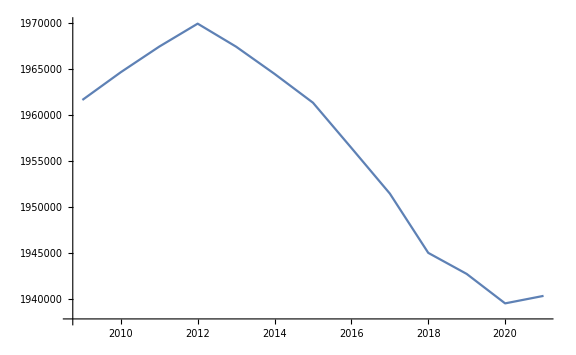

```mathematica
ListLinePlot[poLetihDRS, ImageSize -> Large]
```

### SPOL - SKUPAJ (tuji državljani)

```mathematica
poLetihTujci = graf[Select[#"Četrtletje" == 1.0&], {8, 5}]
```

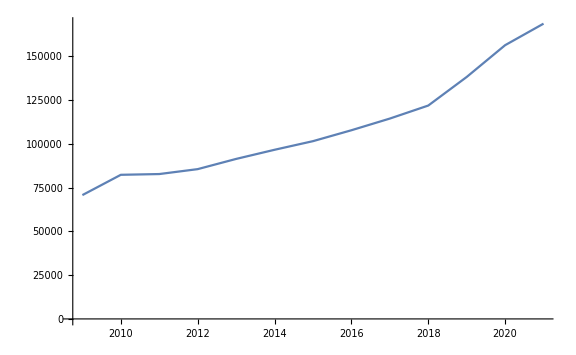

```mathematica
ListLinePlot[poLetihTujci, ImageSize -> Large]
```

## Analiza prebivalstva Slovenije in drugih držav v Mathematici

WolframAlphaQueryParseResults

Slovenia

Z ukazom = population of country, lahko za določeno državo dobimo njeno trenutno prebivaltsvo. Spodaj je primer, ki velja za Slovenijo.

WolframAlphaQueryParseResults

2078932 people

```mathematica
Quantity[2078932, "People"]
```

Z ukazom = population in country in year, lahko za določeno državo in za določeno leto dobimo  število prebivalstva. Spodaj je primer, ki velja za Slovenijo za leto 2016.

WolframAlphaQueryParseResults

2074205 people

#### Funkcija, ki nam vrne število prebivalstva za določeno državo in določeno leto:

```mathematica
steviloPrebivalcev[drzava_, leto_] := Entity["Country",drzava][EntityProperty["Country","Population",{"Date"->DateObject[{leto}]}]]
```

```mathematica
tabela1 = Table[{leto, steviloPrebivalcev["Croatia", leto]}, {leto, 2010, 2020}]
```

{{2010,4328163 people},{2011,4313098 people},{2012,4295869 people},{2013,4276593 people},{2014,4255518 people},{2015,4232874 people},{2016,4208611 people},{2017,4182847 people},{2018,4156407 people},{2019,4130299 people},{2020,4105268 people}}

Graf, ki nam prikaže število prebivalstva za Hrvaško od leta 2000 - 2020.

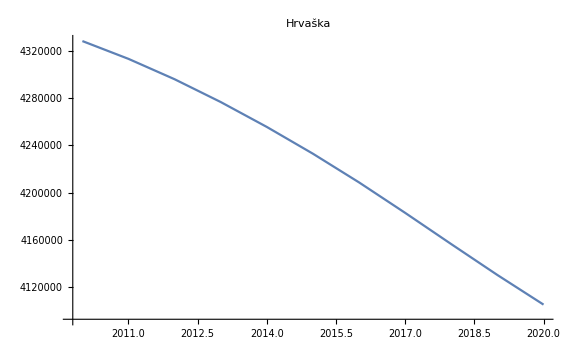

```mathematica
ListLinePlot[{tabela1}, PlotLabel -> "Hrvaška", ImageSize-> Large]
```

```mathematica
tabela2 = Table[{leto, steviloPrebivalcev["Slovenia", leto]}, {leto, 2000, 2020}]
```

{{2000,1987710 people},{2001,1987457 people},{2002,1987265 people},{2003,1987855 people},{2004,1990226 people},{2005,1994979 people},{2006,2002427 people},{2007,2012128 people},{2008,2023049 people},{2009,2033807 people},{2010,2043336 people},{2011,2051278 people},{2012,2057826 people},{2013,2063120 people},{2014,2067488 people},{2015,2071199 people},{2016,2074205 people},{2017,2076395 people},{2018,2077836 people},{2019,2078654 people},{2020,2078932 people}}

Graf, ki nam prikaže celotno prebivalstvo Slovenije od leta 2000 - 2020.

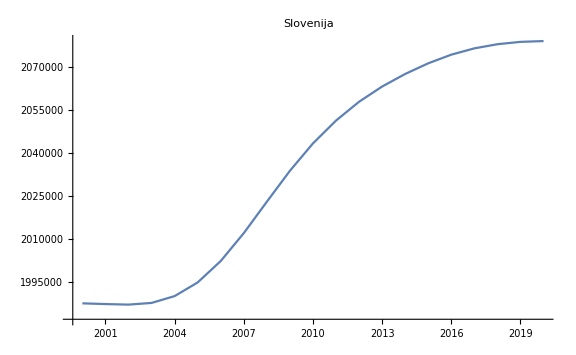

```mathematica
ListLinePlot[{tabela2}, PlotLabel -> "Slovenija",ImageSize-> Large]
```

Graf, ki nam prikaže razliko med prebivalstvom Slovenije in Hrvaške.

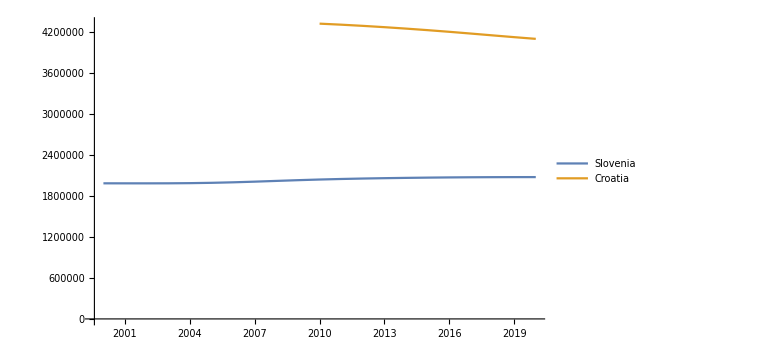

```mathematica
ListLinePlot[{tabela2, tabela1}, PlotLegends-> {"Slovenia", "Croatia"}, ImageSize-> Large]
```

## Analiza glede na relativni priprastek

### Funkcija, ki nam vrne relativni priprastek za določeno državo in leto :

```mathematica
relativniPrirastek[drzava_, leto_] := (steviloPrebivalcev[drzava, leto] - steviloPrebivalcev[drzava, leto - 1]) / steviloPrebivalcev[drzava, leto -1] // N
```

```mathematica
relativniPrirastek["Slovenia", 2020]
```

0.00013374

Relativni prirastki Slovenije, Hrvaške, Španije in Avstrije od leta 2000 - 2020.

```mathematica
relativniSlo = Table[{leto, relativniPrirastek["Slovenia", leto]}, {leto, 2000, 2020}]
```

{{2000,0.0000427646},{2001,-0.000127282},{2002,-0.0000966059},{2003,0.00029689},{2004,0.00119274},{2005,0.00238817},{2006,0.00373337},{2007,0.00484462},{2008,0.00542759},{2009,0.00531772},{2010,0.0046853},{2011,0.00388678},{2012,0.00319216},{2013,0.00257262},{2014,0.00211718},{2015,0.00179493},{2016,0.00145133},{2017,0.00105583},{2018,0.000693991},{2019,0.000393679},{2020,0.00013374}}

```mathematica
relativniHrv = Table[{leto, relativniPrirastek["Croatia", leto]}, {leto, 2000, 2020}]
```

{{2000,-0.00636628},{2001,-0.00451709},{2002,-0.00278376},{2003,-0.00156809},{2004,-0.00114653},{2005,-0.00132554},{2006,-0.00166375},{2007,-0.00191156},{2008,-0.00224371},{2009,-0.00261405},{2010,-0.0030171},{2011,-0.00348069},{2012,-0.00399458},{2013,-0.0044871},{2014,-0.00492799},{2015,-0.00532109},{2016,-0.00573204},{2017,-0.00612173},{2018,-0.00632105},{2019,-0.00628139},{2020,-0.00606034}}

```mathematica
relativniSpa = Table[{leto, relativniPrirastek["Spain", leto]}, {leto, 2000, 2020}]
```

{{2000,0.00915283},{2001,0.0121173},{2002,0.0145249},{2003,0.0161467},{2004,0.0167124},{2005,0.0164119},{2006,0.0161167},{2007,0.0156614},{2008,0.0140822},{2009,0.0111736},{2010,0.00745853},{2011,0.00326503},{2012,-0.000449896},{2013,-0.00281548},{2014,-0.00325219},{2015,-0.0022662},{2016,-0.000809652},{2017,0.00028507},{2018,0.000974073},{2019,0.000940593},{2020,0.000385157}}

```mathematica
relativniAvs = Table[{leto, relativniPrirastek["Austria", leto]}, {leto, 2000, 2020}]
```

{{2000,0.00225559},{2001,0.00352931},{2002,0.0045257},{2003,0.00509589},{2004,0.00500926},{2005,0.00448422},{2006,0.00383939},{2007,0.00342605},{2008,0.00334314},{2009,0.00373229},{2010,0.00445342},{2011,0.00517911},{2012,0.00576436},{2013,0.00634669},{2014,0.00689723},{2015,0.00736628},{2016,0.00790893},{2017,0.00829924},{2018,0.00810451},{2019,0.00716705},{2020,0.00572768}}

Relativno naraščanje prebivalstva za Slovenijo, Hrvaško, Španijo in Avstrijo v letih 2000 - 2020.

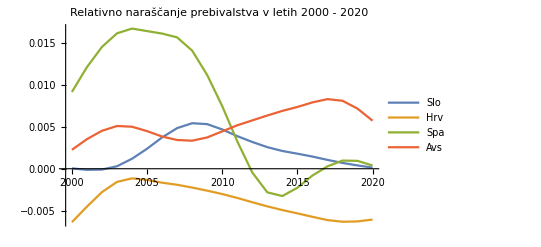

```mathematica
ListLinePlot[{relativniSlo, relativniHrv, relativniSpa, relativniAvs}, PlotLabel -> "Relativno naraščanje prebivalstva v letih 2000 - 2020", PlotLegends -> {"Slo", "Hrv", "Spa", "Avs"}]
```

## Aplikacija v oblaku

```mathematica
narisiPrirastek[drzava_] := ListLinePlot[Table[{leto, relativniPrirastek[drzava, leto]}, {leto, 2000, 2020}], ImageSize-> Large, PlotLabel-> drzava]
```

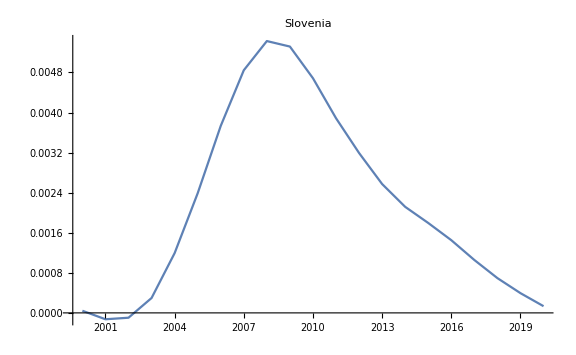

```mathematica
narisiPrirastek["Slovenia"]
```

```mathematica
obrazec = FormPage["Drzava"-> "",narisiPrirastek[#Drzava]&,AppearanceRules-> <|"Title"->"Histogram v odvisnosti od izbrane drzave",
"Description"->"Vnesite ime drzave v Evropi, za katero zelite prikaz. Po potrditvenem gumbu se bo prikazal histrogram, ki bo prikazal relativno narascanje prebivalstva za doloceno drzavo.","SubmitLabel"->"Potrdi"|>]
```

```mathematica
CloudDeploy[obrazec, Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/f3e5373e-589f-4880-8f24-7774f768b8db]